# Input file

```mathematica
filebase="/Users/ailenemacpherson/Documents/VisualStudio/density_dependence";
```

## Parameters

```mathematica
gmax=300;
sampFreq=10;
sel=1; (*1 density-independent, 2 density-dependent*)
geo=1; (*1 metapopulation, 2 expansion*)
init=1 ;(*1 all wild-type, 2 mutation-selection *)
n0=100; (*initial population size*)
```

```mathematica
nLoci=10;
aVec=Table[-0.01,{l,1,nLoci}];
dVec=Table[0,{l,1,nLoci}];
μ=0?.0001;
r=0.5;
```

```mathematica
ρ=0.1;
γ=10;
δ=0.01;
```

```mathematica
ση=0.2;
σMate=0.1;
σMig=0.02;
```

```mathematica
ηKernal[x_]:=ⅇ^(-x^2/(2 ση^2))
MateKernal[x_]:=ⅇ^(-x^2/(2 σMate^2))
```

```mathematica
MigKernal[x_]:=ⅇ^(-x^2/(2 σMig^2))
```

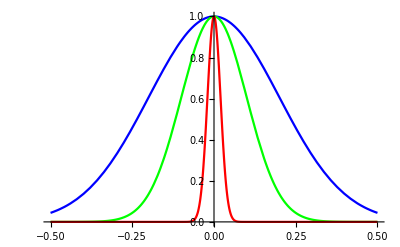

```mathematica
Plot[{ηKernal[x],MateKernal[x],MigKernal[x]},{x,-0.5,0.5},PlotStyle->{Blue,Green,Red},PlotRange->All]
```

## Making output file

```mathematica
out="Input file for density_dependence.\n";
out=out<>"(gmax): "<>ToString[gmax]<>"\n";
out=out<>"(sampFreq): "<>ToString[sampFreq]<>"\n";
out=out<>"(sel): "<>ToString[sel]<>"\n";
out=out<>"(geo): "<>ToString[geo]<>"\n";
out=out<>"(init): "<>ToString[init]<>"\n";
out=out<>"(n0): "<>ToString[n0]<>"\n";
out=out<>"(nLoci): "<>ToString[nLoci]<>"\n";
out=out<>"(aVec): ";
Module[{l},For[l=1,l≤nLoci,l++,out=out<>ToString[aVec[[l]]]<>" "]]
out=out<>"\n(dVec): ";
Module[{l},For[l=1,l≤nLoci,l++,out=out<>ToString[dVec[[l]]]<>" "]]
out=out<>"\n(mu): "<>ToString[μ]<>"\n";
out=out<>"(r): "<>ToString[r]<>"\n";
out=out<>"(rho): "<>ToString[ρ]<>"\n";
out=out<>"(gamma): "<>ToString[γ]<>"\n";
out=out<>"(delta): "<>ToString[δ]<>"\n";
out=out<>"(sigmaEta): "<>ToString[ση]<>"\n";
out=out<>"(sigmaMate): "<>ToString[σMate]<>"\n";
out=out<>"(sigmaMig): "<>ToString[σMig]<>"\n";
```

```mathematica
out
```

Input file for density_dependence.
(gmax): 300
(sampFreq): 10
(sel): 1
(geo): 1
(init): 1
(n0): 100
(nLoci): 10
(aVec): -0.01 -0.01 -0.01 -0.01 -0.01 -0.01 -0.01 -0.01 -0.01 -0.01 
(dVec): 0 0 0 0 0 0 0 0 0 0 
(mu): 0?0.0001
(r): 0.5
(rho): 0.1
(gamma): 10
(delta): 0.01
(sigmaEta): 0.2
(sigmaMate): 0.1
(sigmaMig): 0.02

```mathematica
Export[filebase<>"/Input.txt",out]
```

/Users/ailenemacpherson/Documents/VisualStudio/density_dependence/Input.txt

# Plotting

```mathematica
AFData=Import[filebase<>"/data.csv"];
```

```mathematica
XYData=Import[filebase<>"/xy.csv"];
```

```mathematica
xy[g_]:=Transpose[XYData[[{3g+1,3g+2,3g+3}]]]
```

```mathematica
xyPlot[g_]:=Graphics[{Hue[#3],PointSize[0.01],Point[{#1,#2}]}&@@@xy[g],Frame->True,PlotRange->{{0,1},{0,1}},ImageSize->Medium]
```

```mathematica
pBarData=Transpose[{Table[gen,{gen,0,gmax,sampFreq}],Mean[Transpose[AFData]]}];
```

```mathematica
AFPlot[g_]:=Show[ListLinePlot[pBarData,PlotStyle->Black],ListPlot[{pBarData[[g]]},PlotRange->{0,1},PlotStyle->{Red,PointSize[0.03]}],ImageSize->Medium,PlotLabel->"Allele Frequency"]
```

```mathematica
z[g_,width_]:=BinCounts[XYData[[3g+1]],{0,1,width}]/Total[XYData[[3g+1]]](*Transpose[{Table[(b+width)/2,{b,0,1-width,width}],BinCounts[XYData[[3g+1]],{0,1,width}]/Total[XYData[[3g+1]]]}]*)
```

```mathematica
zAvg[g_]:=Mean[XYData[[3g+1]]]
```

```mathematica
zSD[g_]:=StandardDeviation[XYData[[3g+1]]]
```

```mathematica
zPlot[g_]:=Show[ListLinePlot[Table[{gen,zAvg[gen]+zSD[gen]},{gen,0,Floor[gmax/sampFreq],1}],PlotStyle->Gray,Filling->Axis,FillingStyle->Directive[LightGray,Opacity[0.5]],AxesOrigin->{0,0}],ListLinePlot[Table[{gen,zAvg[gen]-zSD[gen]},{gen,0,Floor[gmax/sampFreq],1}],PlotStyle->Gray,Filling->Axis,FillingStyle->White,AxesOrigin->{0,0}],ListLinePlot[Table[{gen,zAvg[gen]},{gen,0,Floor[gmax/sampFreq],1}],PlotStyle->Black],ListPlot[{{g,zAvg[g]}},PlotRange->{0,1},PlotStyle->{Red,PointSize[0.03]}],PlotRange->{0,1},PlotLabel->"phenotype"]
```

```mathematica
Animate[GraphicsRow[{xyPlot[g],AFPlot[g],zPlot[g]}],{g,0,Floor[gmax/sampFreq],1}]
```

```mathematica
BarLegend[Hue]
```